```mathematica
ClearAll["Global`*"]
f2[n_,k_,f_]:=f2[n,k,f]=Sum[f2[j,k-1,f] f2[n/j,1,f],{j,Divisors[n]}];f2[n_,1,f_]:=f[n];f2[1,1,f_]:=0;f2[n_,0,f_]:=0;f2[1,0,f_]:=1
ff[n_,z_,f_]:=ff[n,z,f]=Sum[FactorialPower[z,a]/a! f2[n,a,f],{a,0,Log[2,n]}]
F2[n_, k_ , f_] := F2[n,k,f]=Sum[ f[j] F2[ Floor[n/j],k-1,f],{j,2,n}];F2[n_,0,f_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
F1[n_,z_,f_]:=Expand[Sum[bins[z,a]F2[n,a,f],{a,0,Log[2,n]}]]
```

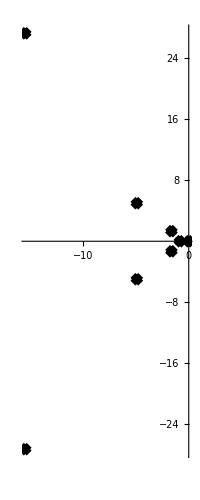

```mathematica
r2[n_] := n
r[n_] := ff[n,1,r2]
RootLocusPlot[1/Expand[F1[400,x,r]],{k,0,1},FeedbackType->None]
```

```mathematica
List@@NRoots[F1[221,x,r]==0,x][[All,2]]
```

{-31.331,-10.6336-6.07118 ⅈ,-10.6336+6.07118 ⅈ,-2.15108-1.86324 ⅈ,-2.15108+1.86324 ⅈ,-0.82962,-0.0199604}

```mathematica
(2E^(I Pi /4 ) )List@@NRoots[F1[331,x,r]==0,x][[All,2]]
```

{-273.542+5.68434×10^-14 ⅈ,0.500292-14.7331 ⅈ,-0.874567-3.50624 ⅈ,-1.3549-0.328372 ⅈ,-1.3549+0.328372 ⅈ,-0.000104393+1.28749×10^-19 ⅈ,-0.874567+3.50624 ⅈ,0.500292+14.7331 ⅈ}

```mathematica
vv:= {-11.199685576035792-12.398224487807212 ⅈ,-11.199685576035792+12.398224487807212 ⅈ,-2.6719503346754907-1.8618449055430242 ⅈ,-2.6719503346754907+1.8618449055430242 ⅈ,-0.9338092178222006,-0.03720467504094745}
```

```mathematica
vv2:={-31.33103586603707,-10.63361495531753-6.07118055234119 ⅈ,-10.63361495531753+6.07118055234119 ⅈ,-2.1510767921924216-1.8632373382027279 ⅈ,-2.1510767921924216+1.8632373382027279 ⅈ,-0.8296202328515756,-0.019960406091375695}
```

```mathematica
Sum[ -1/(j^1),{j,vv2}]
```

52.0095+0. ⅈ

```mathematica
fo[z_] := Product[ (1-(z 3 E^(Pi/8 I ))/j),{j,vv}]
```

```mathematica
fo[1]
```

550.816+1248.13 ⅈ

```mathematica
List@@NRoots[F1[100,x,r]==0,x][[All,2]]
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
List@@NRoots[F1[100,x,r]==0,x][[All,2]]
```

{-9.21723-11.7841 ⅈ,-9.21723+11.7841 ⅈ,-2.20965-1.86061 ⅈ,-2.20965+1.86061 ⅈ,-0.695379,-0.000866226}

```mathematica
g2[n_,k_,s_,f_]:=g2[n,k,s,f]=Sum[g2[j,k-1,s,f] g2[n/j,1,s,f],{j,Divisors[n]}];g2[n_,1,s_,f_]:=f[n,s];g2[1,1,s_,f_]:=0;g2[n_,0,s_,f_]:=0;g2[1,0,s_,f_]:=1
gf[n_,z_,s_,f_]:=gf[n,z,s,f]=Sum[FactorialPower[z,a]/a! g2[n,a,s,f],{a,0,Log[2,n]}]
G2[n_, k_ , s_,f_] := G2[n,k,s,f]=Sum[ f[j,s] G2[ Floor[n/j],k-1,s,f],{j,2,n}];G2[n_,0,s_,f_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
G1[n_,z_,s_,f_]:=Expand[Sum[bins[z,a]G2[n,a,s,f],{a,0,Log[2,n]}]]
```

```mathematica
rr2[n_,s_] := n^-s
rr[n_,s_] := gf[n,1,s,rr2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
List@@NRoots[G1[100,x,0,rr]==0,x][[All,2]]
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
Animate[RootLocusPlot[1/Expand[G1[1000,x,bb ,rr]],{k,0,1},FeedbackType->None],{bb,-3,3,.003}]
```